```mathematica
loadTimeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

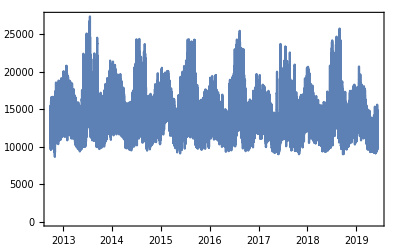

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
toDate[dates_List] := Map[toDate, dates]
toDate[dateObject_DateObject] := DateObject[DateValue[dateObject, {"Year", "Month", "Day"}]];
regroupdataLoad[objects_] := DateListPlot[TimeSeries @ Map[
	{#["Date"], #["Load"]} &,
	objects
]];
regroupdataTemperature[objects_] := DateListPlot[TimeSeries @ Map[
	{#["Date"], #["Temperature"]} &,
	objects
]];
```

```mathematica
allplotsLoad = GroupBy[
	Normal[datasethourandbusinessday], 
	toDate[#Date] &,
regroupdataLoad
];
allplotsTemperature = GroupBy[
	Normal[datasethourandbusinessday], 
	toDate[#Date] &,
regroupdataTemperature
];
```

```mathematica
GraphicsRow[{Manipulate[
allplotsLoad[date],
{date, Keys[allplotsLoad]}
],
Manipulate[
allplotsTemperature[date],
{date, Keys[allplotsTemperature]}
]}]
```

-Graphics-

```mathematica
tsModel=TimeSeriesModelFit[neISOLoad]
```

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

TimeSeriesModel[…]

```mathematica
Normal[%85]
```

ARMAProcess[772.867,{1.64399,-0.698081},{-0.130557,0.157321},230408.]

```mathematica
%85["ParameterTable"]
```

General::munfl: 2.795076180294961298634×10^-12461 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.057476060801311176475×10^-3539 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 1.64399 | 0.00527927 | 311.405 | 0.
𝒶_2 | -0.698081 | 0.00509819 | -136.927 | 0.
𝒷_1 | -0.130557 | 0.0063279 | -20.6319 | 1.5283×10^-94
𝒷_2 | 0.157321 | 0.00512806 | 30.6784 | 2.27716×10^-205

```mathematica
TimeSeriesForecast[neISOLoad
```

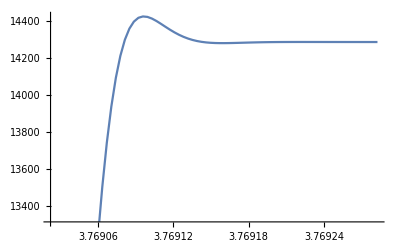

```mathematica
ListLinePlot[TimeSeriesForecast[tsModel,{72}]]
```

```mathematica
p=Predict[neISOLoad,Method->"NeuralNetwork"]
```

Predict::bdfmt: Argument TemporalData[TimeSeries,{{{12986.8,11565.7,11372.9,11483.4,11400.1,11595.1,12040.7,13210.9,14382.8,15156.5,15821.7,16461.2,«27»,18312.1,18302.4,18191.8,17713.9,17151.9,17362.7,16865.2,15888.8,14557.,11521.3,12118.1,«57347»}},{{{«1»}}},«4»,{«1»}},«4»,12.] should be a rule or a list of rules.

Predict[TimeSeries[…],Method→NeuralNetwork]

```mathematica
predictorFunction=Predict[Normal[loadDataDateTime]]
```

Predict::bdfmt: Argument loadDataDateTime should be a rule or a list of rules.

Predict[loadDataDateTime]

```mathematica
ListLinePlot[TimeSeriesForecast[predictorFunction,{72}]]
```

Rule::rhs: Pattern paclet:ref/Information appears on the right-hand side of rule System`ListPlotsDump`modelData[WrappedValues,TimeSeriesForecast[RefLink[Information,paclet:ref/Information][PredictorFunction[TimeSeriesModel[Automatic,{TemporalData[«4»],{«8»},{}}]]],{72.}],Charting`Private`Tag$810041]→TimeSeriesForecast[RefLink[Information,paclet:ref/Information][PredictorFunction[«15»[«9»,«1»]]],«1»].

ListLinePlot::lpn: TimeSeriesForecast[RefLink[Information,paclet:ref/Information][PredictorFunction[TimeSeriesModel[Automatic,{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«3»}},True,12.],{SARIMA,{},ARMA,{},{«1»},{},ARMAProcess[772.867,{«2»},{«2»},230408.],{Rule[«2»],Rule[«2»]}},{}}]]],{72.}] is not a list of numbers or pairs of numbers.

ListLinePlot[TimeSeriesForecast[RefLink[Information,paclet:ref/Information][PredictorFunction[TimeSeriesModel[…]]],{72}]]